# Figure 4

```mathematica
SetDirectory[NotebookDirectory[]];
```

All data were generated with julia code https://github.com/djuliannader/RabiModel.git

#### (a)

```mathematica
Datratio={{1.43765,2.66177159095521/(3*(0.7854369860954992)^2)},{1.4378,1.5169870351760373/(3*(0.7055359738093709)^2)},{1.438,1.4815913320515022/(3*(0.7029937120145018)^2)},{1.44,1.4757657373545028/(3*(0.702558789994917)^2)},{1.8,1.4804338466759013/(3*(0.7038598546251793)^2)},{2,1.4826711454116026/(3*(0.7048231760836707)^2)},{2.16,1.4490049071265219/(3*(0.7061406749154278)^2)},{2.17,1.3863853655159344/(3*(0.7153061207129595)^2)},{2.171,1.4168767416608778/(3*(0.7286635033147801)^2)},{2.172,1.9377147439800826/(3*(0.81222047059144)^2)},{2.173,16.29632763916514/(3*(1.9369682005842725)^2)},{2.174,2.5951275360607524/(3*(0.7651416647091837)^2)},{2.175,1.9414680895647694/(3*(0.72365039016123781)^2)},{2.176,1.7611649433521692/(3*(0.7143596816245358)^2)},{2.177,1.6810601458765666/(3*(0.7108613296386054)^2)},{2.178,1.6366659117420055/(3*(0.709175125110326)^2)},{2.179,1.608712629685433/(3*(0.70823471952626)^2)},{2.18,1.5895896552123816/(3*(0.707657233852783)^2)},{2.19,1.528163567649918/(3*(0.7063076172528544)^2)},{2.2,1.5140183889095455/(3*(0.7061783725725455)^2)},{2.3,1.4987140367214995/(3*(0.7067305556534574)^2)},{2.4,1.4999086428290715/(3*(0.707501450440499)^2)},{2.6,1.5065139051300453/(3*(0.7093556742239)^2)},{2.8,1.5161487996567153/(3*(0.7117376874821352)^2)},{3,1.5292345174415145/(3*(0.7148736811345155)^2)},{3.2,1.5473378581929043/(3*(0.7191500007482132)^2)},{3.4,1.5735669714806557/(3*(0.7252774714763635)^2)},{3.6,1.6144953886255133/(3*(0.7347202949090073)^2)},{3.8,1.6866178199689612/(3*(0.7510542354472962)^2)},{4,1.8463251475360218/(3*(0.7859501826061289)^2)},{4.05,1.921930129865131/(3*(0.8018924424079559)^2)},{4.1,2.0306044987311065/(3*(0.824190700970982)^2)},{4.15,2.2007587218039806/(3*(0.857703849099043)^2)},{4.2,2.509582248375656/(3*(0.9143650905013767)^2)},{4.21,2.627878483040758/(3*(0.9318022666584074)^2)},{4.22,2.723101271334619/(3*(0.9503968037003022)^2)},{4.23,2.8944245388982073/(3*(0.9747821778208932)^2)},{4.24,3.0583462116812927/(3*(1.0023352619908075)^2)},{4.25,3.389205445032044/(3*(1.0427141236615913)^2)},{4.26,3.6455320791573445/(3*(1.08514697318246)^2)},{4.27,4.263144412905323/(3*(1.1589516001374705)^2)},{4.28,9.106777600412286/(3*(1.5379973802228004)^2)},{4.29,5.009305116323149/(3*(1.298401027669174)^2)},{4.3,7.225584732347192/(3*(1.5657773457166166)^2)},{4.31,23.51047646811368/(3*(3.1739957150406455)^2)},{4.32,6.667595376802441/(3*(1.5403661790288146)^2)},{4.33,6.378456792198849/(3*(1.6986147774986553)^2)},{4.34,11.238669257615486/(3*(2.4547048136108063)^2)},{4.35,9.285948647973168/(3*(1.9161226150931423)^2)},{4.36,3.512592777971559/(3*(1.2003200155574583)^2)},{4.37,2.6675184410959742/(3*(1.2170032894196336)^2)},{4.38,3.3189856631886965/(3*(1.4521908723485146)^2)},{4.39,4.556518693535752/(3*(1.7771418513947501)^2)},{4.4,1.3624364588667235/(3*(0.45358134657721205)^2)},{4.45,0.31804071499508635/(3*(0.3307398933663926)^2)},{4.5,0.5781372417233215/(3*(0.444970851723112)^2)},{4.55,0.7627866595933167/(3*(0.5073100003557008)^2)},{4.6,0.8836264103860543/(3*(0.5445846243696765)^2)},{4.65,0.9673876865078146/(3*(0.5691835682981194)^2)},{4.7,1.0285712112683008/(3*(0.5865941751802651)^2)},{4.75,1.0751336341093418/(3*(0.5995540966836929)^2)},{4.8,1.1117218521651822/(3*(0.6095716784669256)^2)},{4.85,1.141213376564446/(3*(0.6175440847287642)^2)},{4.9,1.165479998584639/(3*(0.62403777061109334)^2)},{4.95,1.1857900748055918/(3*(0.6294278340949261)^2)},{5,1.203032871202988/(3*(0.6339724187347134)^2)},{5.1,1.2307161074934383/(3*(0.6412095625125688)^2)},{5.2,1.2519456111035943/(3*(0.646711152203649)^2)},{5.4,1.282303311233143/(3*(0.6545071938969372)^2)},{5.6,1.3028908341150829/(3*(0.6597478045163958)^2)},{5.8,1.3176954398174354/(3*(0.6634939639060021)^2)},{6,1.3287841177848712/(3*(0.6662883359546614)^2)},{6.2,1.3373284849452312/(3*(0.668436462836212)^2)},{6.4,1.344008201226458/(3*(0.6701224488289622)^2)},{6.6,1.3495817651792015/(3*(0.671462718037129)^2)},{6.8,1.3537772781688207/(3*(0.6725319817099877)^2)},{7,1.357159049312992/(3*(0.6733785352303069)^2)},{7.2,1.3597701945404914/(3*(0.6740302369491964)^2)},{7.4,1.361642548573328/(3*(0.6744970061802391)^2)},{7.6,1.362728724525721/(3*(0.674767798375232)^2)},{7.8,1.362850635859937/(3*(0.6747987014587183)^2)},{8,1.3615603661028028/(3*(0.6744783994993284)^2)},{8.2,1.3576970584225454/(3*(0.6735172549155746)^2)},{8.4,1.3474995077888143/(3*(0.6709716392627754)^2)},{8.6,1.309590838785831/(3*(0.6613714408733862)^2)},{8.65,1.2803954285879144/(3*(0.6536845339792502)^2)},{8.7,1.1900318303062452/(3*(0.6359376639835618)^2)},{8.75,0.7846978102188293/(3*(0.5208710571755282)^2)},{8.76,0.5375415287314146/(3*(0.3966211991248306)^2)},{8.768,9.497922092982098/(3*(2.2794644445742347)^2)},{8.77,6.101540958233601/(3*(1.6564279738468262)^2)},{8.78,2.5116437838860572/(3*(0.9368252088903658)^2)},{8.79,1.9905822106458892(3*(0.821985227293116)^2)},{8.8,1.7959198248942703/(3*(0.7776798939976056)^2)},{8.85,1.5411024305093008/(3*(0.7180700255634173)^2)},{8.9,1.4812743936843282/(3*(0.70373370850232)^2)},{9,1.4399069639206517/(3*(0.6937233316052716)^2)},{9.2,1.4156296056331563/(3*(0.687805456898295)^2)},{9.4,1.4073809547613132/(3*(0.6857867214004112)^2)},{9.6,1.403517261516781/(3*(0.6848397162380693)^2)}};
```

```mathematica
Dataratio=Table[{Datratio[[i,1]]/(8.801011),Datratio[[i,2]]},{i,1,Length[Datratio]}];
```

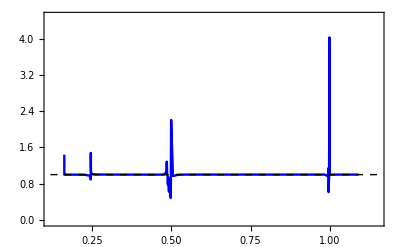

```mathematica
fig4a=Show[ListPlot[Dataratio,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.12,1.15},{-0.05,4.5}},GridLines->{{1/6,0.25,0.5,1},{}},GridLinesStyle->{{Red,Thickness[0.004]},{}},Frame->True,LabelStyle->{18,Black}],Plot[1.466448498970723/(3*0.7002235674837912^2),{x,0.12,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (b)

```mathematica
Datratiop={{1.43765,0.7482511728317965/(3*(0.4062433543824589)^2)},{1.4378,0.399509042325154/(3*(0.36181873676264803)^2)},{1.438,0.38941105865418335/(3*(0.360410502676795)^2)},{1.44,0.3879331481268071/(3*(0.3601649754564568)^2)},{1.8,0.3863439608086134/(3*(0.3595010087652746)^2)},{2,0.38485584727638233/(3*(0.3590219076461521)^2)},{2.16,0.37495289684120436/(3*(0.35895524795381917)^2)},{2.17,0.36358130192578403/(3*(0.36453855700244975)^2)},{2.171,0.37657985079177947/(3*(0.37220263942939896)^2)},{2.172,0.5375628643831135/(3*(0.4186496102620877)^2)},{2.173,4.4762531973568915/(3*(1.0098627609201427)^2)},{2.174,0.6760709622424088/(3*(0.38805087701527224)^2)},{2.175,0.5008690156998623/(3*(0.36681153323704374)^2)},{2.176,0.4534415986905414/(3*(0.3622052329645297)^2)},{2.177,0.4326290844137216/(3*(0.3605239130665569)^2)},{2.178,0.4211945996897211/(3*(0.3597367868640341)^2)},{2.179,(3*(0.3593095750989857)^2)},{2.18,0.4091685720835601/(3*(0.3590536508771601)^2)},{2.19,0.39362314220834005/(3*(0.3584799982335484)^2)},{2.2,0.3899926853443754/(3*(0.3584000101878287)^2)},{2.3,0.3847820323811013/(3*(0.3580505532564072)^2)},{2.4,0.3834375034010616/(3*(0.35766591244948853)^2)},{2.6,0.3811507524647495/(3*(0.35674381599079147)^2)},{2.8,0.3785152833282498/(3*(0.3555651734137215)^2)},{3,0.3751714680673069/(3*(0.3540249007639039)^2)},{3.2,0.3707216538366244/(3*(0.3519458963099424)^2)},{3.4,0.3645064770092295/(3*(0.3490094608893358)^2)},{3.6,0.3552487254355047/(3*(0.34457997301774934)^2)},{3.8,0.3400703401219882/(3*(0.33718073501845)^2)},{4,0.3108152511905364/(3*(0.32240245766761677)^2)},{4.05,0.2987374198575882/(3*(0.3160784331206613)^2)},{4.1,0.28305156124558434/(3*(0.30764271355978284)^2)},{4.15,0.26185777507213953/(3*(0.29578755790932293)^2)},{4.2,0.23161438566719428/(3*(0.2777207679011433)^2)},{4.21,0.23606459469982038/(3*(0.2735268035224528)^2)},{4.22,0.21564683004782828/(3*(0.2673718145355726)^2)},{4.23,0.21214176824151135/(3*(0.2613134500374244)^2)},{4.24,0.19857669930568303/(3*(0.25399166649321187)^2)},{4.25,0.19839325461642707/(3*(0.2455627847527906)^2)},{4.26,0.30783551959002386/(3*(0.24711686221111476)^2)},{4.27,0.22319273168085513/(3*(0.22658862125863763)^2)},{4.28,1.3798624943684032/(3*(0.28707251768236386)^2)},{4.29,0.9958432477724488/(3*(0.28548305963963877)^2)},{4.3,0.9148999621429108/(3*(0.24554188119770323)^2)},{4.31,6.853151860730768/(3*(0.7683505986301614)^2)},{4.32,5.401199142944598/(3*(0.8254869678274537)^2)},{4.33,2.98106475011136/(3*(0.5126987869196142)^2)},{4.34,4.945432931138579/(3*(0.7318370288368984)^2)},{4.35,13.833242879246054/(3*(2.337601775128362)^2)},{4.36,3.512592777971559/(3*(1.3351488655432675)^2)},{4.37,4.779801041061898/(3*(0.9844570276896767)^2)},{4.38,4.6330242724922845/(3*(0.9677714299324532)^2)},{4.39,5.517684215092675/(3*(1.1561468997426074)^2)},{4.4,7.23024030724348/(3*(2.072323873510602)^2)},{4.45,1.6374956881039546/(3*(0.778786114091589)^2)},{4.5,0.9371301360625817/(3*(0.5669018542692883)^2)},{4.55,0.7328331356793495/(3*(0.49720403765829074)^2)},{4.6,0.6399644299485827/(3*(0.46339649773143965)^2)},{4.65,0.587590447301273/(3*(0.44354062514229936)^2)},{4.7,0.5541346556365275/(3*(0.43049959342062766)^2)},{4.75,0.5309700309291392/(3*(0.421285691217679)^2)},{4.8,0.514003620515355/(3*(0.41443272314805607)^2)},{4.85,0.5010522113118796/(3*(0.4091379793402944)^2)},{4.9,0.49084755751978953/(3*(0.4049253930345933)^2)},{4.95,0.48260352361441206/(3*(0.4014948345619453)^2)},{5,0.47580729671103206/(3*(0.39864774663165353)^2)},{5.1,0.4652673658770568/(3*(0.39419718267669146)^2)},{5.2,0.4574802119305985/(3*(0.3908805887992634)^2)},{5.4,0.44676597008233326/(3*(0.386276306926167)^2)},{5.6,0.43976761029988604/(3*(0.3832423959300918)^2)},{5.8,0.43486196146311595/(3*(0.38110301477594455)^2)},{6,0.4312534600152699/(3*(0.37952283290616634)^2)},{6.2,0.42850656574110474/(3*(0.3783170657066284)^2)},{6.4,0.42635511260731546/(3*(0.37737617716918387)^2)},{6.6,0.4247326473382143/(3*(0.3766310736454861)^2)},{6.8,0.4233667555069774/(3*(0.37603922594526756)^2)},{7,0.4223066218006351/(3*(0.37557184752184486)^2)},{7.2,0.42149460710608416/(3*(0.3752128004719081)^2)},{7.4,0.420914556579401/(3*(0.37495602072695067)^2)},{7.6,0.4205782600579702/(3*(0.37480715132490006)^2)},{7.8,0.4205389875346018/(3*(0.374790038174301)^2)},{8,1.3615603661028028/(3*(0.6744783994993284)^2)},{8.2,0.4221263573708255/(3*(0.37549452584569887)^2)},{8.4,0.42531114891789984/(3*(0.3769024319585569)^2)},{8.6,0.4377210923943334/(3*(0.3823096054238859)^2)},{8.65,0.44831902724463424/(3*(0.38675276751794097)^2)},{8.7,0.46547949151823653/(3*(0.3976674192258115)^2)},{8.75,0.6790608390431903/(3*(0.48580760722727573)^2)},{8.76,1.1887912415772992/(3*(0.6853097180454782)^2)},{8.768,0.6662618451061901/(3*(0.2982544094197565)^2)},{8.77,0.2434809252666748/(3*(0.20817334313748107)^2)},{8.78,0.21419516992619983/(3*(0.2722340685154405)^2)},{8.79,0.28098341530338683/(3*(0.3086092558009889)^2)},{8.8,0.3154746917484532/(3*(0.3258282034653259)^2)},{8.85,0.37145131363468437/(3*(0.3524692487176215)^2)},{8.9,0.38681784526207214/(3*(0.3595589079882065)^2)},{9,0.3980477354950827/(3*(0.36468380435583164)^2)},{9.2,0.40489311178968584/(3*(0.36778375991549966)^2)},{9.4,0.4072647831750278/(3*(0.3688533737211679)^2)},{9.6,0.4083836740690294/(3*(0.36935721189306975)^2)}};
```

```mathematica
Dataratiop=Table[{Datratiop[[i,1]]/(8.801011),Datratiop[[i,2]]},{i,1,Length[Datratiop]}];
```

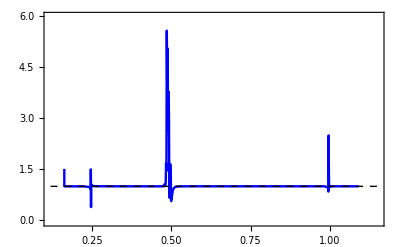

```mathematica
fig4b=Show[ListPlot[Dataratiop,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.12,1.15},{-0.05,6}},GridLines->{{1/6,0.25,0.5,1},{}},GridLinesStyle->{{Red,Thickness[0.004]},{}},Frame->True,LabelStyle->{18,Black}],Plot[1.466448498970723/(3*0.7002235674837912^2),{x,0.12,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (c)

```mathematica
Datpur={{1.43765,0.9933527494406048},{1.4378,0.9939617883933407},{1.438,0.9939808838571469},{1.44,0.9939840545604032},{1.8,0.9939716172180049},{2,0.9939628093958185},{2.16,0.9939471400229626},{2.17,0.9938576325787606},{2.171,0.9937401732388036},{2.172,0.9930408397555518},{2.173,0.9844498558181207},{2.174,0.9935359901247801},{2.175,0.9938412797130615},{2.176,0.99390607834518},{2.177,0.9939291662423819},{2.178,0.9939396786044137},{2.179,0.993945201000637},{2.18,0.99390483835044198},{2.19,0.9939540332749865},{2.2,0.9939536873642564},{2.3,0.9939469990991234},{2.4,0.993940111581821},{2.6,0.9939240174139341},{2.8,0.9939035440607767},{3,0.9938766919872954},{3.2,0.993840147655041},{3.4,0.9937878454448081},{3.6,0.9937073177262004},{3.8,0.9935681742071859},{4,0.9932715260458058},{4.05,0.9931362969197296},{4.1,0.9929474818586389},{4.15,0.9926644644375624},{4.2,0.9921882805681049},{4.21,0.9920437960183752},{4.22,0.9918872841151444},{4.23,0.9916860044786037},{4.24,0.9914562923249891},{4.25,0.9911277525004414},{4.26,0.9907747802854138},{4.27,0.9901771340084724},{4.28,0.9872672274831625},{4.29,0.9890090490196962},{4.3,0.9868512651202641},{4.31,0.9742478398675603},{4.32,0.9870123734532766},{4.33,0.9855843384293019},{4.34,0.9793780928288868},{4.35,0.9839352331359915},{4.36,0.9897199691181096},{4.37,0.989484168310679},{4.38,0.987451178571527},{4.39,0.9846835119910133},{4.4,0.996211234466161},{4.45,0.997208285274764},{4.5,0.9962057649326731},{4.55,0.9956636810230934},{4.6,0.9953408223417639},{4.65,0.9951282521513838},{4.7,0.9949780380242651},{4.75,0.9948663539247824},{4.8,0.994780104618593},{4.85,0.9947115148954685},{4.9,0.994655682258465},{4.95,0.994609364045394},{5,0.9945703303841835},{5.1,0.9945082103141947},{5.2,0.9944610255985478},{5.4,0.9943942362510872},{5.6,0.9943494100605722},{5.8,0.9943174227791454},{6,0.9942936108538474},{6.2,0.9942753494119471},{6.4,0.9942610540449932},{6.6,0.994249757982159},{6.8,0.9942407595686198},{7,0.9942336844351206},{7.2,0.994228286325874},{7.4,0.9942244791840268},{7.6,0.9942223570653224},{7.8,0.9942222956524223},{8,0.9942252479474886},{8.2,0.9942336943498835},{8.4,0.994255718561624},{8.6,0.9943382299853093},{8.65,0.9944042997740141},{8.7,0.9945543068731445},{8.75,0.9955464930713109},{8.76,0.9966388903783129},{8.768,0.9807528633533986},{8.77,0.9859361939057166},{8.78,0.9919922928281378},{8.79,0.9929676777973113},{8.8,0.9933449135745905},{8.85,0.9938534732468524},{8.9,0.9939760206732551},{9,0.9940617210575275},{9.2,0.9941125827165618},{9.4,0.9941301060289334},{9.6,0.9941384676807977}};
```

```mathematica
Dataimp=Table[{Datpur[[i,1]]/(8.801011),1-Datpur[[i,2]]},{i,1,Length[Datpur]}];
```

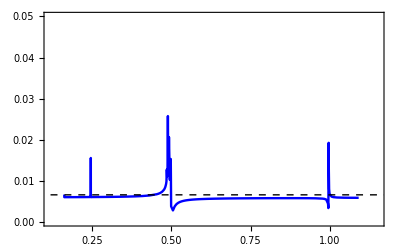

```mathematica
fig4c=Show[ListPlot[Dataimp,Joined->True,PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.12,1.15},{0.0,0.05}},GridLines->{{1/6,0.25,0.5,1},{}},GridLinesStyle->{{Red,Thickness[0.004]},{}},Frame->True,LabelStyle->{18,Black}],Plot[1-0.9934136182043661,{x,0.12,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (d)

```mathematica
Datnn={{1.43765,0.10213964004409326},{1.4378,0.006180404397177375},{1.438,0.0007185854186317897},{1.44,9.813615404496989*10^-5},{1.8,0.0037534943181130043},{2,0.0036342628098346985},{2.16,0.0014794895509175898},{2.17,0.005929708605961537},{2.171,0.01629766138316424},{2.172,0.08141534340153678},{2.173,0.5219203964998027},{2.174,0.042022232243011715},{2.175,0.009925687096497882},{2.176,0.0034962468907218103},{2.177,0.0015269944032589855},{2.178,0.0006667513587870211},{2.179,0.00031689696489678454},{2.18,0.00017432542044582},{2.19,1.2591*10^-5},{2.2,2.516524*10^-5},{2.3,0.003994306117855784},{2.4,0.0038692193124505447},{2.6,0.003728521712607291},{2.8,0.0036380677722100963},{3,0.0035305723949896617},{3.2,0.003403702857674995},{3.4,0.0032329925106564517},{3.6,0.0029887771724737},{3.8,0.002611042726570423},{4,0.0019907103157235095},{4.05,0.0017545368415605722},{4.1,0.0014758260442511162},{4.15,0.001181909944742321},{4.2,8.945691*10^-5},{4.21,0.003123400225836024},{4.22,0.001039707257270761},{4.23,0.007688159169442876},{4.24,0.00497444339962283},{4.25,0.012846634068778284},{4.26,0.05045177417112745},{4.27,0.0346524610682164},{4.28,0.20363517697743472},{4.29,0.15008163422405985},{4.3,0.1558113308797553},{4.31,0.5748690496110065},{4.32,0.43975991527245495},{4.33,0.3119883911000165},{4.34,0.4721643804540283},{4.35,0.7227049848716758},{4.36,0.4681091606950456},{4.37,0.3714889955785583},{4.38,0.39055046302023366},{4.39,0.46268646059985086},{4.4,0.3002622904372383},{4.45,0.007554379743763606},{4.5,0.0004987800772968676},{4.55,0.000159747990006065},{4.6,0.000190843444878519},{4.65,9.726027*10^-5},{4.7,0.00018524700965505403},{4.75,0.00037475208156068085},{4.8,0.0004707097392422366},{4.85,0.0005168751356214862},{4.9,0.0005550700117313845},{4.95,0.0005871766616005747},{5,0.0006145307951188617},{5.1,0.0006448748561624917},{5.2,0.000677354908038108},{5.4,0.000645229037751438},{5.6,0.0006372058093395694},{5.8,0.0006202142452862436},{6,0.0006369563026660252},{6.2,0.0006497895093662276},{6.4,0.0006595137199021384},{6.6,0.000669379878651899},{6.8,0.000675092827463919},{7,0.00068008890510729},{7.2,0.0006839823871827022},{7.4,0.0006867776513899138},{7.6,0.0006883958741890073},{7.8,0.00068856407101614},{8,0.0006866059038055372},{8.2,0.0006807748306121297},{8.4,0.0006654455606480703},{8.6,0.0006103246580499988},{8.65,0.0006116795388300122},{8.7,0.00024625038603198757},{8.75,0.0007065867215267918},{8.76,0.027337669608767712},{8.768,0.22844386271153594},{8.77,0.08581217166627497},{8.78,0.00140630680043774},{8.79,0.0007204460138958702},{8.8,0.0017021458338943862},{8.85,0.0033576011252822724},{8.9,0.0038209695390944987},{9,0.004185613102762886},{9.2,0.004394607558311225},{9.4,0.004467410594464649},{9.6,0.004501826842757239}};
```

```mathematica
Dataneg=Table[{Datnn[[i,1]]/(8.801011),Datnn[[i,2]]},{i,1,Length[Datnn]}];
```

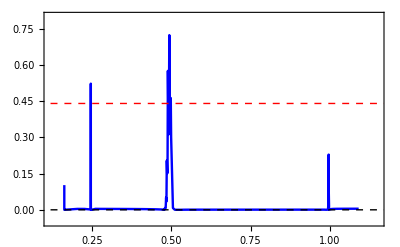

```mathematica
fig4d=Show[ListPlot[Dataneg,Joined->True,PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.12,1.15},{-0.05,0.8}},GridLines->{{1/6,1/4,1/2,1},{}},GridLinesStyle->{{Red,Thickness[0.004]},{}},Frame->True,LabelStyle->{18,Black}],Plot[00,{x,0.12,1.5},PlotStyle->{Dashed,Black,Thick}],Plot[0.44,{x,0.12,1.5},PlotStyle->{Dashed,Red,Thick}]]
```

#### (e)

```mathematica
Datfisdis={{1.43765,1.5502085500120806},{1.4378,1.3941353854341512},{1.438,1.389162499839122},{1.44,1.3883114118212108},{1.8,1.3908477203292815},{2,1.3927265528529675},{2.16,1.3952822873245212},{2.17,1.4131290983397538},{2.171,1.4391761651152788},{2.172,1.6019800972828946},{2.173,3.7565943374805384},{2.174,1.5107139252854709},{2.175,1.382118818569585},{2.176,1.4114340867229573},{2.177,1.4045804974139933},{2.178,1.401274557468325},{2.179,1.3994294912807075},{2.18,1.3982956742582475},{2.19,1.3956391813180653},{2.2,1.395381488819788},{2.3,1.3964521508545817},{2.4,1.3979559214073416},{2.6,1.4015744437871198},{2.8,1.4062232833620614},{3,1.4123433609488099},{3.2,1.4206880065747003},{3.4,1.432642963337933},{3.6,1.4510616047971816},{3.8,1.4829080278869753},{4,1.5508871314634258},{4.05,1.5819174063318848},{4.1,1.625291857104569},{4.15,1.6904221231357395},{4.2,1.8003791686550765},{4.21,1.8341851550960278},{4.22,1.870200470070952},{4.23,1.917417827891255},{4.24,1.970709807239547},{4.25,2.0487636776085454},{4.26,2.1306308047816804},{4.27,2.2728421746459126},{4.28,2.9990399138063557},{4.29,2.5403291378531443},{4.3,3.050244418924804},{4.31,6.026694727495723},{4.32,3.001640639391336},{4.33,3.3001424426662274},{4.34,4.708759485131133},{4.35,3.710660018429782},{4.36,2.3516525848573506},{4.37,2.3830383066689054},{4.38,2.8317628696796415},{4.39,3.445794397438575},{4.4,0.9003694991684559},{4.45,0.6577962886547093},{4.5,0.8832128480392878},{4.55,1.0058577384950145},{4.6,1.0790663748486593},{4.65,1.1273286246210836},{4.7,1.1614632305245},{4.75,1.1868589001667298},{4.8,1.206481263970348},{4.85,1.2220928101527055},{4.9,1.2348056418400977},{4.95,1.24535576089102},{5,1.2542495294335918},{5.1,1.2684098623599198},{5.2,1.2791721052682783},{5.4,1.29441945831698},{5.6,1.30466682598768},{5.8,1.311990991367831},{6,1.3174538174738295},{6.2,1.3216530321193136},{6.4,1.3249487202301649},{6.6,1.3275686860283906},{6.8,1.3296588149265214},{7,1.3313136862967165},{7.2,1.3325877525305707},{7.4,1.3335004196004636},{7.6,1.3340301201501525},{7.8,1.3340910520296827},{8,1.3334656835442864},{8.2,1.331587968634119},{8.4,1.3266135666790677},{8.6,1.3078483825253522},{8.65,1.2928186276030331},{8.7,1.2580954107598663},{8.75,1.03250212116051},{8.76,0.787931425211135},{8.768,4.384826777952892},{8.77,3.2204674894715573},{8.78,1.8438639502192937},{8.79,1.6210048351745223},{8.8,1.5347916961373158},{8.85,1.418592158373959},{8.9,1.3906108364466714},{9,1.3710649331059082},{9.2,1.3595072584148529},{9.4,1.3555645723163838},{9.4,1.3537153129501949}};
```

```mathematica
Datafisdis2=Table[{Datfisdis[[i,1]]/(8.801011),Datfisdis[[i,2]]},{i,1,Length[Datfisdis]}];
```

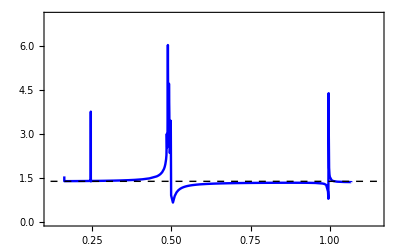

```mathematica
fig4e=Show[ListPlot[Datafisdis2,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.12,1.15},{0.0,7}},GridLines->{{1/6,0.25,0.5,1},{}},GridLinesStyle->{{Red,Thickness[0.004]},{}},Frame->True,LabelStyle->{18,Black}],Plot[1.382118818569585,{x,0.12,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (f)

```mathematica
Datfis={{1.43765,4.932186874422668},{1.4378,2.175427800875245},{1.438,1.9025658993979282},{1.44,1.8509991137529302},{1.8,1.8505934887047815},{2,1.8490726520594976},{2.16,1.8059491659279359},{2.17,2.050910986159062},{2.171,2.4098520132203936},{2.172,3.298437030033955},{2.173,3.5102030571196767},{2.174,3.681261552045513},{2.175,2.935939537410965},{2.176,2.544070205623636},{2.177,2.337317480779564},{2.178,2.217155783271115},{2.179,2.1410414605022092},{2.18,2.089467845215173},{2.19,1.933712460767559},{2.2,1.9017950442484914},{2.3,1.8664960385937475},{2.4,1.8639326692699272},{2.6,1.8646713220813504},{2.8,1.8676055593779266},{3,1.871999643574576},{3.2,1.878121586618649},{3.4,1.8867555776942242},{3.6,1.8995347771044053},{3.8,1.9202005117147356},{4,1.959971455501754},{4.05,1.9769119701239874},{4.1,1.9999844628286758},{4.15,2.0344193373051063},{4.2,2.0963696092899555},{4.21,2.127328073625103},{4.22,2.1428023654901818},{4.23,2.2258853680212685},{4.24,2.2292125002925958},{4.25,2.384247128936587},{4.26,2.7014800928611877},{4.27,2.6301940357461886},{4.28,4.481004478220652},{4.29,3.3962900879621967},{4.3,3.1243651487379553},{4.31,3.4372136653003698},{4.32,4.168709991057375},{4.33,2.8833798300909965},{4.34,2.337359526275622},{4.35,2.402373242787396},{4.36,2.9482683291328056},{4.37,2.4172533463404684},{4.38,1.797095781362147},{4.39,1.2854825556686007},{4.4,1.2790291107257277},{4.45,1.9031033658101442},{4.5,1.4217919139162614},{4.55,0.12656382339696487},{4.6,0.8318712123965564},{4.65,1.2313341847643302},{4.7,1.413129572312737},{4.75,1.5118487473316222},{4.8,1.572901426105342},{4.85,1.614151648240974},{4.9,1.643815149702035},{4.95,1.6661459582907179},{5,1.6835529110212906},{5.1,1.7089162700037872},{5.2,1.7264932163209599},{5.4,1.749228743553875},{5.6,1.7632559885481782},{5.8,1.7727308619806796},{6,1.7795180423735204},{6.2,1.7845704038146801},{6.4,1.7883671496376983},{6.6,1.7918081388142084},{6.8,1.7940368046693607},{7,1.7958874541899517},{7.2,1.7973115329495408},{7.4,1.7983287768372753},{7.6,1.7989186797356767},{7.8,1.7989888866274675},{8,1.798297763901672},{8.2,1.796202996251919},{8.4,1.790550928027511},{8.6,1.768087702369015},{8.65,1.749616564191876},{8.7,1.6703619034380972},{8.75,1.1969655948420455},{8.76,2.4316374200275117},{8.768,1.4557571862502476},{8.77,1.77661022694027},{8.78,1.9826997334002845},{8.79,1.9580578493921093},{8.8,1.933160961063201},{8.85,1.87384880286276},{8.9,1.8528873764038005},{9,1.8361554177700403},{9.2,1.8253609265138622},{9.4,1.8215195685502292},{9.6,1.819692235241883}};
```

```mathematica
Datafisher=Table[{Datfis[[i,1]]/(8.801011),Datfis[[i,2]]},{i,1,Length[Datfis]}];
```

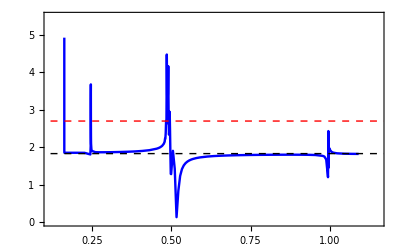

```mathematica
fig4f=Show[ListPlot[Datafisher,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.12,1.15},{0,5.5}},GridLines->{{1/6,0.25,0.5,0.998},{}},GridLinesStyle->{{Red,Thickness[0.004]},{}},Frame->True,LabelStyle->{18,Black}],Plot[1.8283437968627987,{x,0.12,1.5},PlotStyle->{Dashed,Black,Thick}],Plot[2.7,{x,0.12,1.5},PlotStyle->{Dashed,Red,Thick}]]
```

#### (g)

```mathematica
DatexpH0={{1.43765,-25.096809362395888},{1.4378,-25.14026020121981},{1.438,-25.141641684230756},{1.44,-25.14188085909532},{1.8,-25.141883522963813},{2,-25.141879647993658},{2.16,-25.141620914396537},{2.17,-25.1366035405585},{2.171,-25.12939099875359},{2.172,-25.0846498867483},{2.173,-24.491141088679054},{2.174,-25.111004501750834},{2.175,-25.132752047507697},{2.176,-25.137586157838975},{2.177,-25.13939322619058},{2.178,-25.140259097344032},{2.179,-25.140739701795262},{2.18,-25.141033822493664},{2.19,-25.141727778895554},{2.2,-25.141816049679463},{2.3,-25.141869657793354},{2.4,-25.14186748176166},{2.6,-25.14185639720481},{2.8,-25.14183777658868},{3,-25.14180699459292},{3.2,-25.14175397998379},{3.4,-25.14165637409764},{3.6,-25.14145748486601},{3.8,-25.14098057015407},{4,-25.13944063908771},{4.05,-25.138520440632043},{4.1,-25.137025296989634},{4.15,-25.134358953546304},{4.2,-25.128839252025518},{4.21,-25.126434693630987},{4.22,-25.12474069923317},{4.23,-25.121467327286265},{4.24,-25.118034368942393},{4.25,-25.11176243560136},{4.26,-25.100054036005687},{4.27,-25.09112969689072},{4.28,-24.960611387431708},{4.29,-25.025858119124084},{4.3,-24.976305911563472},{4.31,-24.293588561898172},{4.32,-24.693327693657984},{4.33,-24.81028602458807},{4.34,-24.505602796397497},{4.35,-23.839966562011824},{4.36,-24.52725773857145},{4.37,-24.699380881187693},{4.38,-24.64800209,-24.470908064708887},{4.4,-24.34820022088411},{4.45,-25.0270760062257},{4.5,-25.10410113352826},{4.55,-25.12311632606387},{4.6,-25.130540009949534},{4.65,-25.134206886384483},{4.7,-25.136293703062996},{4.75,-25.137599135705283},{4.8,-25.138472948098567},{4.85,-25.139088352992815},{4.9,-25.139539271955304},{4.95,-25.13988031214168},{5,-25.140145031696434},{5.1,-25.14052463136181},{5.2,-25.140779622363244},{5.4,-25.141092820837823},{5.6,-25.141272492248685},{5.8,-25.141386072881883},{6,-25.141462850277694},{6.2,-25.141517295456136},{6.4,-25.14155725451967},{6.6,-25.141587231053116},{6.8,-25.141610066080514},{7,-25.14162740874672},{7,-25.141640295362787},{7.4,-25.141649235525147},{7.6,-25.141654230435197},{7.8,-25.141654567581202},{8,-25.14164810078335},{8.2,-25.14162871285389},{8.4,-25.14157411622322},{8.6,-25.141319801183577},{8.65,-25.1410582550916},{8.7,-25.140152133220344},{8.75,-25.125386170990296},{8.76,-25.057056168671657},{8.768,-24.768378799780795},{8.77,-24.97348315556851},{8.78,-25.125938568606493},{8.79,-25.13713244079959},{8.8,-25.139850949532427},{8.85,-25.14176317012664},{8.9,-25.141880088110685},{9,-25.141873864159116},{9.2,-25.141834565725507},{9.4,-25.14181477367151},{9.6,-25.141804214434046}};
```

```mathematica
DataexpH0=Table[{DatexpH0[[i,1]]/(8.801011),DatexpH0[[i,2]]/50},{i,1,Length[DatexpH0]}];
```

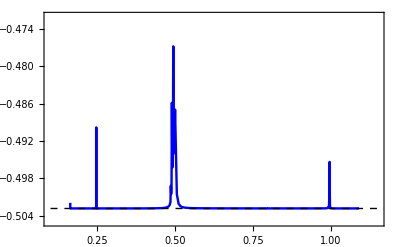

```mathematica
fig4g=Show[ListPlot[DataexpH0,Joined->True,
PlotStyle->{Blue,Thickness[0.0043]},PlotRange->{{0.1,1.15},{-0.505,-0.472}},GridLines->{{1/6,1/4,1/2,1},{}},GridLinesStyle->{{Red,Thickness[0.004]},{}},Frame->True,LabelStyle->{18,Black}],Plot[-25.142253953183587/50,{x,0.1,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

#### (h)

```mathematica
DatF1={{1.43765,0.9896893901121767},{1.4378,0.9996200529018111},{1.438,0.9999357904197341},{1.44,0.9999904475225222},{1.8,0.9999895330977169},{2,0.9999871880804628},{2.16,0.9998967431624342},{2.17,0.9981641368400065},{2.171,0.9956735704865795},{2.172,0.9802239208738867},{2.173,0.7752756410673627},{2.174,0.9893241205204745},{2.175,0.9968339422844015},{2.176,0.9985032540197913},{2.177,0.999127268709701},{2.178,0.9994262678725587},{2.179,0.999592225539811},{2.18,0.9996937857393962},{2.19,0.9999333474603569},{2.2,0.9999637428832394},{2.3,0.999981248007366},{2.4,0.999979235057437},{2.6,0.9999718157392854},{2.8,0.9999595564914098},{3,0.9999391522498321},{3.2,0.9999036943515439},{3.4,0.9998378511912095},{3.6,0.9997026717196871},{3.8,0.9993765305198856},{4,0.9983195883166138},{4.05,0.9976882351394726},{4.1,0.9966645677168037},{4.15,0.9948484156642581},{4.2,0.9911403301801764},{4.21,0.9898778573744087},{4.22,0.9884492264995394},{4.23,0.9865424857371834},{4.24,0.9842303199403363},{4.25,0.9808624419985759},{4.26,0.9765272416488741},{4.27,0.9699855948855745},{4.28,0.9356979618866367},{4.29,0.9503608947166396},{4.3,0.9212480350262187},{4.31,0.7163628357960885},{4.32,0.8793680550488481},{4.33,0.8641369968609347},{4.34,0.7222594675929269},{4.35,0.5719089565926511},{4.36,0.8078153959576194},{4.37,0.8388251511888929},{4.38,0.7784703904730617},{4.39,0.6533577253121863},{4.4,0.5090729753510663},{4.45,0.9229450098137715},{4.5,0.9740506644303933},{4.55,0.9869810551560666},{4.6,0.9920833814973701},{4.65,0.9946185641719897},{4.7,0.9960668199823266},{4.75,0.9969752477718361},{4.8,0.9975845843434054},{4.85,0.9980144511884497},{4.9,0.9983298743285188},{4.95,0.9985687351251814},{5,0.9987543502416412},{5.1,0.9990209034669628},{5.2,0.9992002805938938},{5.3,0.9993273818119766},{5.4,0.9994211056202988},{5.6,0.9995481546033073},{5.8,0.9996286879749112},{6,0.9996832711570923},{6.2,0.9997220817438673},{6.4,0.9997506410241775},{6.6,0.9997721733633831},{6.8,0.999788592714859},{7,0.999801125598848},{7.2,0.9998104922965363},{7.4,0.9998170500220395},{7.6,0.999820795143965},{7.8,0.9998212152741482},{8,0.999816775248095},{8.2,0.9998031099700018},{8.4,0.9997643580442837},{8.6,0.9995840726350917},{8.65,0.9993997744111401},{8.7,0.9987785064210728},{8.75,0.9884251454091615},{8.76,0.9407424478279836},{8.768,0.7401553393523722},{8.77,0.8829272560885213},{8.78,0.9889588516387746},{8.79,0.9967219450503717},{8.8,0.9986014030634531},{8.85,0.9999133063233463},{8.9,0.9999897526811296},{9,0.9999819513102106},{9.2,0.9999526636385317},{9.4,0.9999383677169446},{9.6,0.9999308943227435}};
DatF3={{1.43765,1.41420333672052*10^-6},{1.4378,1.3350300298389073*10^-6},{1.438,1.3451607057712124*10^-6},{1.44,1.3572099910753032*10^-6},{1.8,3.3381382415179907*10^-6},{2,5.359764409373884*10^-6},{2.16,8.060841168692888*10^-6},{2.17,9.512464183141844*10^-6},{2.171,1.0451785371171067*10^-5},{2.172,1.368818377344753*10^-5},{2.173,3.469839892941838*10^-7},{2.174,4.574651730450348*10^-6},{2.175,6.042047849281713*10^-6},{2.176,6.645949090359748*10^-6},{2.177,6.978868878787963*10^-6},{2.178,7.1932825267928226*10^-6},{2.179,7.345493117822192*10^-6},{2.18,7.4610534229953715*10^-6},{2.19,8.00076713033175*10^-6},{2.2,8.285545409555136*10^-6},{2.3,1.056897077101392*10^-5},{2.4,1.3279314983852472*10^-5},{2.6,2.0929911216329763*10^-5},{2.8,3.322055362280333*10^-5},{3,5.360782165213989*10^-5},{3.2,8.901430064131825*10^-5},{3.4,0.00015475414787405345},{3.6,0.00028970214987471027},{3.8,0.0006151090940714215},{4,0.0016674021014264002},{4.05,0.002294099377238349},{4.1,0.0033069136745774905},{4.15,0.005092690790682448},{4.2,0.008686472857294857},{4.21,0.009839048264658984},{4.22,0.011239580113385363},{4.23,0.012966082292333484},{4.24,0.01511664645820116},{4.25,0.017933167367622935},{4.26,0.021252709037553347},{4.27,0.026651423281744583},{4.28,0.03709989944677973},{4.29,0.03840829283953336},{4.3,0.05875718243197936},{4.31,0.11288430495823641},{4.32,0.033020837163934204},{4.33,0.09292600854835618},{4.34,0.18476138537752837},{4.35,0.06843592675921728},{4.36,5.670146164554855*10^-5},{4.37,0.03467933906524085},{4.38,0.11245810372321238},{4.39,0.23670602845922917},{4.4,0.4323702168373696},{4.45,0.0740408194128825},{4.5,0.02546448328768818},{4.55,0.012871578799858488},{4.6,0.007853171473050228},{4.65,0.005347059745939597},{4.7,0.003911164721158761},{4.75,0.003008777744215613},{4.8,0.0024027061165668257},{4.85,0.001974743446091294},{4.9,0.0016604988347890981},{4.95,0.0014224029715026554},{5,0.0012373039844996736},{5.1,0.000971367839926927},{5.2,0.0007923201092456885},{5.3,0.000665408309055599},{5.4,0.0005717996152453495},{5.6,0.0004448711980559351},{5.8,0.0003643912717409454},{6,0.00030983314818078516},{6.2,0.00027103499727789527},{6.4,0.00024248751437734906},{6.6,0.00022091976146801741},{6.8,0.0002045132865466007},{7,0.00019197908741798675},{7.2,0.00018260889613393186},{7.4,0.00017604685319602372},{7.6,0.00017229708879395604},{7.8,0.0001718722677274811},{8,0.00017630769530745195},{8.2,0.0001899681132020914},{8.4,0.00022871003459251461},{8.6,0.0004088340745607748},{8.65,0.0005924638313348188},{8.7,0.0011976240620605483},{8.75,0.01156952418207588},{8.76,0.059253577070594685},{8.768,0.25982128271648863},{8.77,0.11705572534321772},{8.78,0.011031573213471826},{8.79,0.0032696816226177737},{8.8,0.0013906890703056706},{8.85,7.940645251273118*10^-5},{8.9,3.100885757829489*10^-6},{9,1.0991065952966946*10^-5},{9.2,4.0320778754704914*10^-5},{9.4,5.4625219618021434*10^-5},{9.6,6.209879747114854*10^-5}};
DatF5={{1.43765,2.3225297929974996*10^-7},{1.4378,2.447496721083398*10^-10},{1.438,3.761517187908834*10^-9},{1.44,7.492751534407777*10^-9},{1.8,6.001741483153633*10^-8},{2,3.826027999117827*10^-7},{2.16,8.805563111317178*10^-5},{2.17,0.0018186089450039644},{2.171,0.004307433207927819},{2.172,0.01974905988444434},{2.173,0.22465145154777258},{2.174,0.01066135710996681},{2.175,0.0031521616892005314},{2.176,0.001482691059130755},{2.177,0.0008585024617724545},{2.178,0.0005593616351733124},{2.179,0.0003932902576202969},{2.18,0.0002916369248877334},{2.19,5.1579414881649125*10^-5},{2.2,2.0901309071651504*10^-5},{2.3,1.1063040739897207*10^-6},{2.4,4.0265286288422963*10^-7},{2.6,1.5565132221971722*10^-7},{2.8,1.0248860574951947*10^-7},{3,8.949980003538008*10^-8},{3.2,9.913307104370012*10^-8},{3.4,1.4192503179858004*10^-7},{3.6,2.7984281900512884*10^-7},{3.8,8.520368104503413*10^-7},{4,5.1421786073412515*10^-6},{4.05,9.612404462000129*10^-6},{4.1,2.014053336969419*10^-5},{4.15,4.9667799870734755*10^-5},{4.2,0.0001590677476134063},{4.21,0.00020993321124009875},{4.22,0.0002861527250972273},{4.23,0.0004043471459392848},{4.24,0.0005780340760628797},{4.25,0.0009151215654854631},{4.26,0.001163706246510048},{4.27,0.0024466172683292823},{4.28,0.00917313588003482},{4.29,0.0025147992411110077},{4.3,0.012643551391242399},{4.31,0.09209659046873427},{4.32,0.01239476884508969},{4.33,0.00138202034221273},{4.34,0.032437492625413275},{4.35,0.25805507328236865},{4.36,0.15498066211375328},{4.37,0.10939948668103207},{4.38,0.09823735359060026},{4.39,0.10150157618303576},{4.4,0.055753587047436014},{4.45,0.0029462157149492386},{4.5,0.00047459002848520545},{4.5,0.00014115661195226176},{4.6,5.765662348845641*10^-5},{4.65,2.8542316441932606*10^-5},{4.7,1.607459976647212*10^-5},{4.75,9.93071939442783*10^-6},{4.8,6.577434745850139*10^-6},{4.85,4.599263796919433*10^-6},{4.9,3.3586958234075278*10^-6},{4.95,2.541326716914468*10^-6},{5,1.9804344560786425*10^-6},{5.1,1.2911567014322923*10^-6},{5.2,9.061465771355322*10^-7},{5.3,6.725681820669749*10^-7},{5.4,5.21500014935309*10^-7},{5.6,3.4576909778747834*10^-7},{5.8,2.517622947521255*10^-7},{6,1.9538043858911636*10^-7},{6.2,1.5786262060430318*10^-7},{6.4,1.2539761232039838*10^-7},{6.6,1.4343170276121378*10^-7},{6.8,1.156844803987374*10^-7},{7,1.0418751143807025*10^-7},{7.2,9.664983367868561*10^-8},{7.4,9.162496134210473*10^-8},{7.6,8.872625419191606*10^-8},{7.8,8.812224968550631*10^-8},{8,9.079304562334736*10^-8},{8.2,1.0000506295208923*10^-7},{8.4,1.301249914312807*10^-7},{8.6,3.8195990973048365*10^-7},{8.65,.127700584439899*10^-6},{8.7,1.7403885992303933*10^-5},{8.75,4.108236868388365*10^-8},{8.76,1.5058926337268865*10^-8},{8.768,9.276706846163585*10^-7},{8.77,5.493600454811352*10^-7},{8.78,1.198012452246278*10^-7},{8.79,5.355429644905914*10^-8},{8.8,2.804031767415668*10^-8},{8.85,4.864085472790662*10^-10},{8.9,1.6664781208176824*10^-9},{9,1.01618964032814*10^-8},{9.2,2.1381464173185925*10^-8},{9.4,2.688297236285814*10^-8},{9.6,2.981849888531349*10^-8}};
```

```mathematica
.
```

```mathematica
DataF1=Table[{DatF1[[i,1]]/(8.801011),DatF1[[i,2]]},{i,1,Length[DatF1]}];
DataF3=Table[{DatF3[[i,1]]/(8.801011),DatF3[[i,2]]},{i,1,Length[DatF3]}];
DataF5=Table[{DatF5[[i,1]]/(8.801011),DatF5[[i,2]]},{i,1,Length[DatF5]}];
```

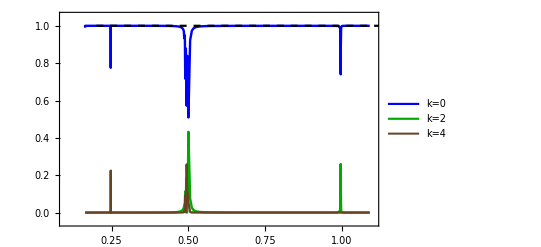

```mathematica
fig4h=Show[ListPlot[{DataF1,DataF3,DataF5},Joined->True,PlotRange->{{0.1,1.1},{-0.05,1.05}},GridLines->{{1/6,1/4,1/2,1},{}},GridLinesStyle->{{Red,Thickness[0.004]},{}},Frame->True,PlotStyle->{{Blue,Thickness[0.0043]},{Darker[Green],Thickness[0.0043]},{Darker[Brown],Thickness[0.004]}},PlotLegends->{"k=0","k=2","k=4"},LabelStyle->{18,Black}],Plot[1,{x,0.2,1.5},PlotStyle->{Dashed,Black,Thick}]]
```

```mathematica
Export["Fidelities.png",fig4h]
```

Fidelities.png